```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
<<GDCAnalysis3`
<<GDCComparisons`
```

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

```mathematica
filesAR=FileNames["/home/carla/GDC/CH_Pool/PHI/GDC_CHP_AR_PHI_ALL_Out/*.txt"];
inputAR=Map[Get[#]&, filesAR];
dojAR=inputAR[[All,1]];
zAR=inputAR[[All,2]];
fAR=inputAR[[All,3]];
filesBR=FileNames["/home/carla/GDC/CH_Pool/PHI/GDC_CHP_BR_PHI_ALL_Out/*.txt"];
inputBR=Map[Get[#]&, filesBR];
dojBR=inputBR[[All,1]];
zBR=inputBR[[All,2]];
fBR=inputBR[[All,3]];
```

```mathematica
(*MIN Values*)
Map[dojBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[zBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[fBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
```

{0.,0.,0.,0.,0.,0.}

{-1,-1,-1,-1,-1,-1}

{-1,-1,-1,-1,-1,-1}

```mathematica
tsAR={2,3,4,5,6,7,8};
tsBR={2.5,3.5,4.5,5.5,6.5,7.5};
tsAll=Union[tsAR,tsBR];
```

```mathematica
dojMax=maxValFunc[tsAR, tsBR, dojAR, dojBR, "PHI", "DOJ"]
zMax=maxValFunc[tsAR, tsBR, zAR, zBR, "PHI", "Z"]
fMax=maxValFunc[tsAR, tsBR, fAR, fBR, "PHI", "F"]
```

{{2,0.00154049},{2.5,0.00154049},{3,0.010101},{3.5,0.010101},{4,0.0333333},{4.5,0.0439691},{5,0.0222222},{5.5,0.0133333},{6,0.0133333},{6.5,0.0133333},{7,0.04},{7.5,0.0416667},{8,1.}}

{{2,0.000854832},{2.5,0.000874688},{3,0.00966208},{3.5,0.00964112},{4,0.0331088},{4.5,0.0436414},{5,0.0220912},{5.5,0.0132806},{6,0.0132806},{6.5,0.0132813},{7,0.0399493},{7.5,0.0416165},{8,1.}}

{{2,0.478626},{2.5,0.49525},{3,0.916712},{3.5,0.912907},{4,0.98662},{4.5,0.988765},{5,0.988275},{5.5,0.992127},{6,0.992127},{6.5,0.99222},{7,0.99747},{7.5,0.997595},{8,1}}

```mathematica
dojTat=Get["/home/carla/GDC/CONF/PHI/PHI_DOJ.txt"]
zTat=Get["/home/carla/GDC/CONF/PHI/PHI_Z.txt"]
fTat=Get["/home/carla/GDC/CONF/PHI/PHI_F.txt"]
```

{{2,0.000880282},{2.5,0.000880282},{3,0.00505051},{3.5,0.00505051},{4,0.0333333},{4.5,0.0231729},{5,0.0222222},{5.5,0.0133333},{6,0.0133333},{6.5,0.0133333},{7,0.04},{7.5,0.0416667},{8,1.}}

{{2,0.0005698},{2.5,0.000583039},{3,0.0047545},{3.5,0.0047396},{4,0.0331008},{4.5,0.0230405},{5,0.0220897},{5.5,0.0132801},{6,0.0132801},{6.5,0.0132807},{7,0.0399488},{7.5,0.0416159},{8,1.}}

{{2,0.478516},{2.5,0.49514},{3,0.889273},{3.5,0.88402},{4,0.986146},{4.5,0.988635},{5,0.98814},{5.5,0.99204},{6,0.99204},{6.5,0.992133},{7,0.997442},{7.5,0.997567},{8,1}}

```mathematica
(*dojPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "PHI"},PlotStyle->{Red, Blue},PlotLabel->"DOJ : CH=MAX vs. CH=PHI geg EV&BK=PHI",PlotMarkers->{{"X",12}, {"P",12}},ImageSize->400];
zPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "PHI"},PlotStyle->{Red, Blue},PlotLabel->"Z : CH-MAX vs. CH_PHI geg EV&BK=PHI",PlotMarkers->{{"X",12}, {"P",12}},ImageSize->400];
fPlot=ListLogPlot[{fMax,fTat},PlotLegends->{"MAX", "PHI"},PlotStyle->{Red, Blue},PlotLabel->"F : CH-MAX vs. CH_PHI geg EV&BK=PHI",PlotMarkers->{{"X",12}, {"P",12}},ImageSize->400];
confMAX=Column[{dojPlot,zPlot,fPlot}]*)
```

```mathematica
(* dojBR[[5,2]][["value"]]
dojTat[[10]]
dojBR[[5,2]][["list"]][[1;;3]]
Map[compCHMaxFunc[First[persMixFunc["PHI"]], #, tatCH , dojBR]&,{4.5}]
Map[vvPosFunc[First[persMixFunc["PHI"]],# , tatCH, "CH", "PEN"]&,{4.5}]
Map[vvPosFunc[First[persMixFunc["PHI"]],# , dojBR,  "CH", "PEN"]&,{4.5}]*)
```

```mathematica
tatCH=Map[Get[#]&,FileNames["/home/carla/GDC/POS/*.txt"]];
persInd=First[persMixFunc["PHI"]]
pers="PHI";
```

11

```mathematica
(*VV-Value von CH-TAT : Ähnlichkeit von CH-TAT mit DEV*)
Map[{#,vvPosFunc[persInd,# , tatCH, "CH", "PEN"]}&,tsAR]
```

{{2,0.6},{3,0.6},{4,0.8},{5,0.8},{6,0.8},{7,0.8},{8,1.}}

```mathematica
(*Veritistic Value von CH-MAX : Ähnlichkeit von CH_MAX mit DEV*)
dojVV=vvCHMaxFunc[tsAR, tsBR, dojAR, dojBR,pers];
zVV=vvCHMaxFunc[tsAR, tsBR, zAR, zBR,pers];
fVV=vvCHMaxFunc[tsAR, tsBR, fAR, fBR,pers];
dojVVHist=vvHistPointsFunc[dojVV];
zVVHist=vvHistPointsFunc[zVV];
fVVHist=vvHistPointsFunc[fVV];
```

13

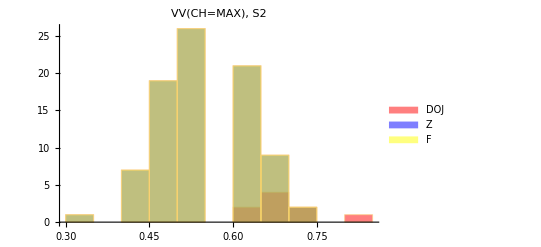
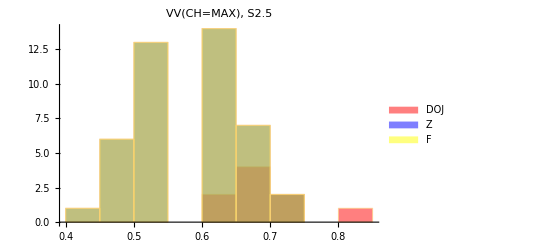
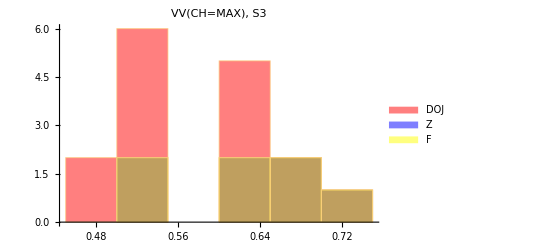
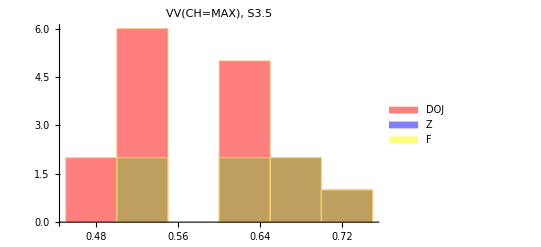
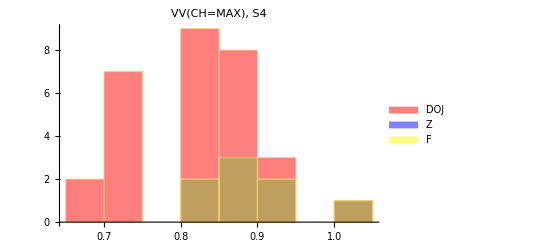
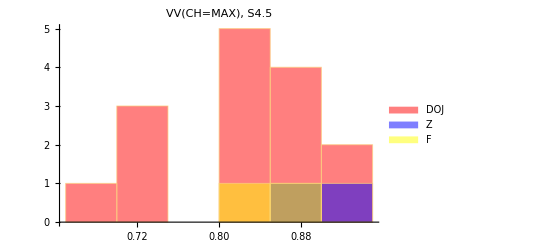
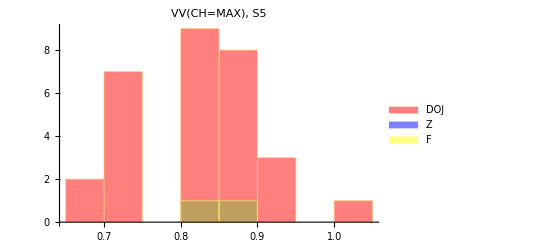
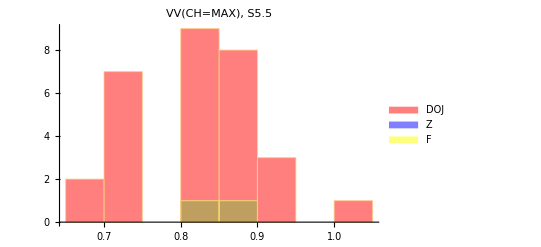
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | GrayLevel[1] | GrayLevel[1]

```mathematica
(*ListPlot[dojVVHist,PlotLegends->{"DOJ"},PlotStyle->{Red},PlotLabel->"VV CH=MAX geg EV&BK=PHI",PlotMarkers->{{"D",12}}, PlotRange->All]
ListPlot[zVVHist, PlotLegends->{"Z"},PlotStyle->{Blue},PlotLabel->"VV CH=MAX geg EV&BK=PHI",PlotMarkers->{{"Z",12}}, PlotRange->All]
ListPlot[fVVHist, PlotLegends->{"F"},PlotStyle->{Green},PlotLabel->"VV CH=MAX geg EV&BK=PHI",PlotMarkers->{{"F",12}}, PlotRange->All]
vvMaxPlot=ListPlot[{dojVVHist,zVVHist,fVVHist}, PlotLegends->{"DOJ","Z","F"},PlotStyle->{Red,Blue,Green},PlotLabel->"VV CH=MAX geg EV&BK=PHI",PlotMarkers->{{"D",12},{"Z",12},{"F",12}}, PlotRange->{0,1.05}]*)
timL={2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8};
Length[timL]
hist=Map[Histogram[{dojVV[[#,2]],zVV[[#,2]],fVV[[#,2]]}, PlotLabel->"VV(CH=MAX),    S"<>ToString[timL[[#]]],ImageSize->400, ChartLegends->{"DOJ","Z","F"},ChartStyle->{Red,Blue,Yellow}]&,Range[Length[timL]]];
histOut=Grid[{hist[[1;;3]],hist[[4;;6]],hist[[7;;9]],hist[[10;;12]],{hist[[13]],White,White}},ItemSize->35]
```

```mathematica
SetDirectory["/home/carla/GDC/CH_Pool/PHI/"];
(*Export["COMP_DOJ_CHTAT_CHMAX_PHI.jpeg",dojPlot,ImageResolution->300]
Export["COMP_CHTAT_CHMAX_PHI.jpeg",confMAX,ImageResolution->300]*)
Put[dojVVHist, "gdc_DOJ_VV_CHMAX_PHI.txt"]
Put[zVVHist, "gdc_Z_VV_CHMAX_PHI.txt"]
Put[fVVHist, "gdc_F_VV_CHMAX_PHI.txt"]
Export["VV_CHMAX_HIST_PHI.jpeg",histOut,ImageResolution->300]
```

VV_CHMAX_HIST_PHI.jpeg